# Homework 10

Name: Eslam Muhammed Ahmed Zenhom

ID: 201700788

## Problem 1: Fig 7.12

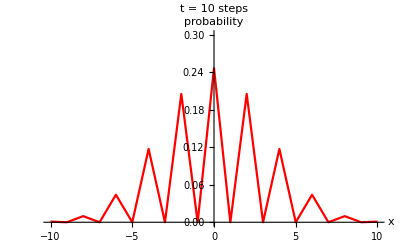

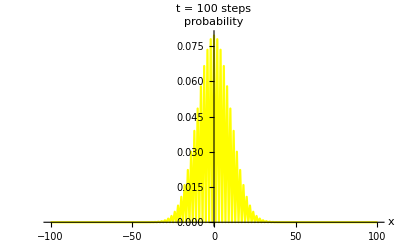

```mathematica
ClearAll["Global`*"];
t=11;
P = Table[0,{i,-10,10,1},{j,1,t,1}];
(*starting from the origin*)
P[[11,1]]=1;
Do[Do[P[[i,n]]=0.5*(P[[i-1,n-1]]+P[[i+1,n-1]]);
P[[1,n]]=0.5*P[[2,n-1]];P[[21,n]]=0.5*P[[20,n-1]],{i,2,20}],{n,2,t}];
pp=Table[0,{i,21}];
Do[
pp[[i]]={i-11,P[[i,t]]},{i,1,21,1}];
p1=ListPlot[pp,PlotRange->{{-10,10},{0,0.3}},PlotLabel->"t = 10 steps",
AxesLabel->{"x","probability"}, Joined -> {True},PlotStyle-> Red]
(*The 100 steps case*)
t1=101;
P1 = Table[0,{i,-100,100,1},{j,1,t1,1}];
P1[[101,1]]=1;
Do[
Do[
P1[[i,n]]=0.5*(P1[[i-1,n-1]]+P1[[i+1,n-1]]);P1[[1,n]]=0.5*P1[[2,n-1]];P1[[201,n]]=0.5*P1[[200,n-1]],{i,2,200}],{n,2,t1}];
pp1=Table[0,{i,201}];
Do[
pp1[[i]]={i-101,P1[[i,t1]]},{i,1,201,1}];
p11=ListPlot[pp1,PlotLabel->" t = 100 steps",AxesLabel->{"x","probability"},PlotRange->{{-100,100},{0,0.08}},Joined -> {True}, PlotStyle-> Yellow]
```

## Problem 2: 10.1

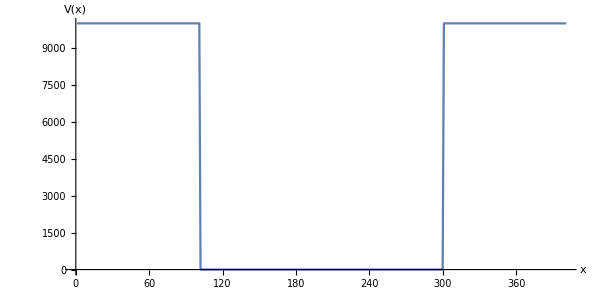

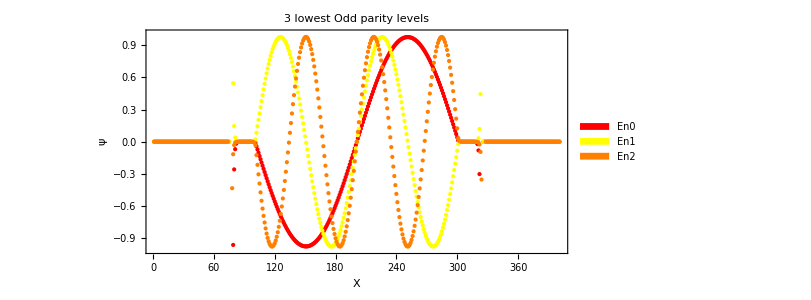

Exact Energies for the first 5 odd levels are:
 {4.9348, 19.7392, 44.4132, 78.9568, 123.37}
estimated values from computations using the shooting method were:
{4.89847, 19.5891, 44.0575, 78.2796, 122.222}

{1.2337,11.1033,30.8425,60.4513,99.9297}

Exact Energies for the first 5 even levels are:
 {1.2337, 11.1033, 30.8425, 60.4513, 99.9297}
estimated values from computations using the shooting method were:
{1.21258, 10.9115, 30.2999, 59.3589, 98.0605}

{1.21258,10.9115,30.2999,59.3589,98.0605}

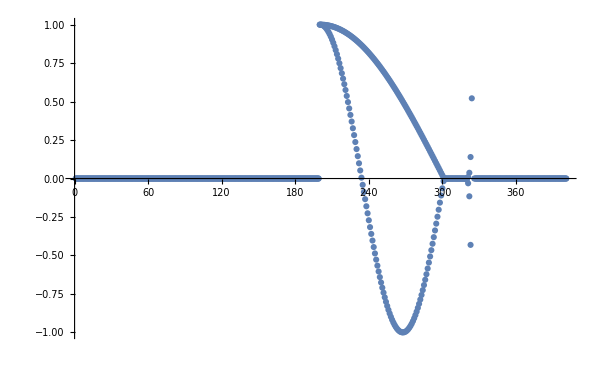

```mathematica
(*The odd solution*)
ClearAll["Global`*"]
xMax = 2.0; dx = 0.01; 
x = Range[-xMax, xMax, dx]; lx = Length[x];
v = Table[0.0, {i,lx}];
potEng = 10000.0;

Do[
If[x[[i]]<= -1.0, v[[i]] = potEng];
If[x[[i]]>= 1.0, v[[i]] = potEng];
If[x[[i]]== 0.0,i0 = i]; (* i0 = central position of the well *)
,{i,lx}];
nEng = 5; (* number of energy levels *)
color={Red,Yellow,Orange,Green,Magenta};
labels={"En0","En1","En2","En3","En4"};
engOddList = Table[0.0, {i,nEng}];
plot = Table[0.0, {i,nEng}];

eng = 1.0; (* first guess for E *)
psiMax = 2.0; (* top bound for psi *)

Do[
dE = .4; (* first guess for dE *) 

(* Obtaining the sign of the initial psi RIGHT*)
psi = Table[0.0, {i,lx}];
psi[[i0]] = 0.0; psi[[i0 -1]] = -dx*j;  (* δx slope at x = 0 and 0.0 ψ at x=0*)
i=i0+1;
While[Abs[psi[[i-1]]] < psiMax && i < lx,
psi[[i]] = 2.0 psi[[i-1]] - psi[[i-2]] - 2.0 (eng - v[[i-1]])psi[[i-1]] dx^2;  i++];
psiLastR=psi[[i-1]] ; (* Last value of psi before quitting *)

(* Main loop for energy levels *)
While[Abs[dE] >0.000000000001,
psi = Table[0.0, {i,lx}];
psi[[i0]] = 0.0; psi[[i0 -1]] = -dx*j; psi[[i0 +1]] = dx*j;  (* δx slope at x = 0 and 0.0 ψ at x=0*)

(*multiply dx by J as a systematic way for increasing the slope of ψ around x=0 with higher E values, to accomodate higher slopes for increasing E values and avoid the probability amplitudes falling off with larger E's as the frequncies increase*)

i=i0+2;
While[Abs[psi[[i-1]]] < psiMax && i < lx,
psi[[i]] = 2.0 psi[[i-1]] - psi[[i-2]] - 2.0 (eng - v[[i-1]])psi[[i-1]] dx^2;  i++];
psiNewR=psi[[i-1]] ;
If[Sign[psiNewR] == Sign[psiLastR], eng = eng + dE]; 
If[Sign[psiNewR] != Sign[psiLastR],dE=-dE/2.0; eng = eng + dE];
psiLastR = psiNewR];
(*--------------------------------------------------------------------------*)

dEl=0.4;
While[Abs[dEl] > 0.000000000001,
k=i0-2;
While[Abs[psi[[k+1]]] < psiMax && k > 0,
psi[[k]] = 2.0 psi[[k+1]] - psi[[k+2]] - 2.0 (eng - v[[k+1]])psi[[k+1]] dx^2;  k--];
psiNewL=psi[[k+1]] ;
If[Sign[psiNewL] == Sign[psiLastL], eng = eng - dEl]; (*used negative here to reverse direction*)
If[Sign[psiNewL] != Sign[psiLastL],dEl=-dEl/2.0; eng = eng + dEl];
psiLastL = psiNewL];

(*--------------------------------------------------------------------------*)

engOddList[[j]] = eng;
eng = eng + 0.5;

(*divide ψ by 0.328, which is the amplitude we found before normalization*)

plot[[j]]=ListPlot[psi/0.328,PlotRange->All,PlotStyle->{color[[j]],PointSize->0.005},PlotLegends->SwatchLegend[{color[[j]]},{labels[[j]]}]]
,{j,nEng}];


leg=SwatchLegend[{Red,Yellow,Orange},{"E0","E1","E2"}];
engOddList (* Calculations using shooting method *);
engExact =Table[((2.0n ) Pi/2.0)^2/2.0,{n,5}] ;

(* Exact .. corrected, since the odd functions have different integers or half integers of pi in their equation*)
ListPlot[v, Joined->True, AxesLabel->{"x","V(x)"},AspectRatio->0.5,ImageSize->600]
Show[plot[[1]],plot[[2]],plot[[3]],PlotRange-> {-1,1},AspectRatio->0.5,ImageSize->600,Frame -> True, FrameLabel->{Style["X",FontSize->15],Style["ψ",FontSize->20]},PlotLabel->"3 lowest Odd parity levels"]

Print["Exact Energies for the first 5 odd levels are:\n " <>ToString [engExact]<>"\nestimated values from computations using the shooting method were:\n" <>ToString[engOddList]]
(*--------------------------------------------------------------------------*)
(*--------------------------------------------------------------------------*)
(*The even solution*)
ClearAll["Global`*"]
xMax = 2.0; dx = 0.01; 
x = Range[-xMax, xMax, dx]; lx = Length[x];
v = Table[0.0, {i,lx}];
potEng = 10000.0;
Do[
If[x[[i]]<= -1.0, v[[i]] = potEng];
If[x[[i]]>= 1.0, v[[i]] = potEng];
If[x[[i]]== 0.0,i0 = i]; (* i0 = central position of the well *)
,{i,lx}];
nEng = 5; (* number of energy levels *)
engEvenList = Table[0.0, {i,nEng}];
plot = Table[0.0, {i,nEng}];

eng = 1.0; (* first guess for E *)
psiMax = 2.0; (* top bound for psi *)

Do[
dE = .4; (* first guess for dE *) 

(* Obtaining the sign of the initial psi *)
psi = Table[0.0, {i,lx}];
psi[[i0]] = 1.0; psi[[i0 -1]] = 1.0;  (* zero slop at x = 0 *)
i=i0+1;
While[Abs[psi[[i-1]]] < psiMax && i < lx,
psi[[i]] = 2.0 psi[[i-1]] - psi[[i-2]] - 2.0 (eng - v[[i-1]])psi[[i-1]] dx^2;  i++];
psiLast=psi[[i-1]] ; (* Last value of psi before quitting *)

(* Main loop for energy levels *)
While[Abs[dE] > 0.000000000001,
psi = Table[0.0, {i,lx}];
psi[[i0]] = 1.0; psi[[i0 -1]] = 1.0;  (* zero slop at x = 0 *)
i=i0+1;
While[Abs[psi[[i-1]]] < psiMax && i < lx,
psi[[i]] = 2.0 psi[[i-1]] - psi[[i-2]] - 2.0 (eng - v[[i-1]])psi[[i-1]] dx^2;  i++];
psiNew=psi[[i-1]] ;
If[Sign[psiNew] == Sign[psiLast], eng = eng + dE]; 
If[Sign[psiNew] != Sign[psiLast],dE=-dE/2.0; eng = eng + dE];
psiLast = psiNew];
engEvenList[[j]] = eng;
eng = eng + 0.5;
plot[[j]]=ListPlot[psi,PlotRange->All]
,{j,nEng}];

(* Results *)
engExact =Table[((2.0n -1) Pi/2.0)^2/2.0,{n,5}] (* Exact *)
Print["Exact Energies for the first 5 even levels are:\n " <>ToString [engExact]<>"\nestimated values from computations using the shooting method were:\n" <>ToString[engEvenList]]
engEvenList (* Calculations using shooting method *)

ListPlot[v, Joined->True, AxesLabel->{"x","V(x)"}];
Show[plot[[1]],plot[[2]],PlotRange-> {-1,1}]
```

## Problem 3: 10.2

0.497186

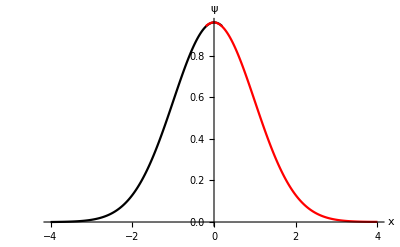

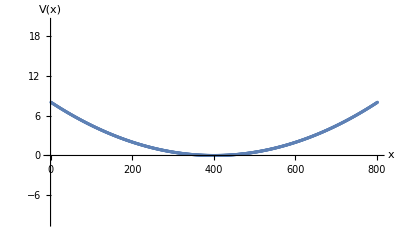

1.49435

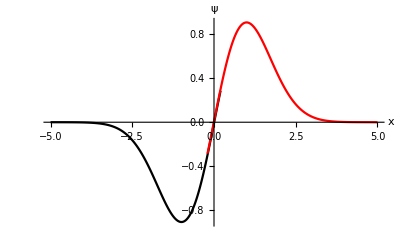

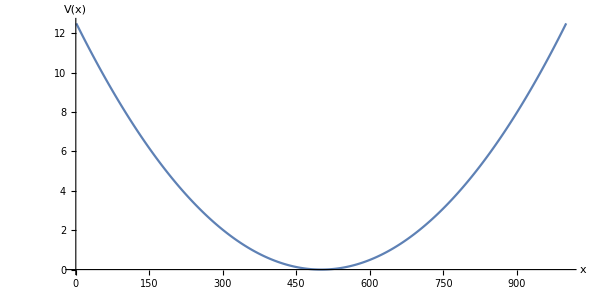

The exact Energies for the first 5 odd levels are:
 {0.5,1.5,2.5,3.5,4.5}
estimated values from computations using the shooting method were:
{0.499997, 1.49998, 2.49996, 3.49992, 4.49988}

```mathematica
(*I solved the problem using the shotting because I couldn't solve using the matching at first. But then I solved using both. *)
(*Firstly using hte matching method energy*)
(*First energy*)
ClearAll["Global`*"];
dx = 0.01; xMin = -4;xMax = 4; 
x = Range[xMin,xMax,dx]; lx = Length[x];
eng =0.45; (* first guess for E *)

dE = .02; (* first guess for dE *) 

vLJ[x_,m_,w_]:= 1/2*m *w^2*x^2;
v = Table[1/2 i^2, {i,-xMax,xMax,dx}]; (* harmonic potential *)
iMin = Position[v,Min[v]][[1,1]]; (* Minimum potential position *)

iOverLap = 20; (* determines number of overlapping steps *)
(* Initialization of ψL and ψR;
ψL runs from the beginging of x to iOverLap steps beyond the minimum position of the potential; 
ψR runs iOverLap steps before the minimum till the end;
 ψL and ψR overlaps on 2 × iOverLap points on the x axis;
 *)
psiL = Table[0.0, {i,iMin + iOverLap}]; 
lL = Length[psiL];
psiR = Table[0.0, {i,iMin - iOverLap,lx}]; 
lR = Length[psiR];

(* Start with a small slope by giving the following values to the first elements in each psi. We keep the second elements zeros. So we start from the third elements *)
psiL[[1]] = -0.0001 dx; psiR[[1]] =psiL[[1]]; 

(* Obtaining the slopes of the initial psi *)

Do[psiL[[i]] = 2.0 psiL[[i-1]] - psiL[[i-2]] - 2.0 (eng - v[[i-1]])psiL[[i-1]] dx^2  
,{i,3,lL}];
Do[psiR[[i]] = 2.0 psiR[[i-1]] - psiR[[i-2]] - 2.0 (eng - v[[1-i]])psiR[[i-1]] dx^2  
,{i,3,lR}]; (* v is reversed: not i - 1, but -(i - 1) *)
psiR = Reverse[psiR]; (* reverse the elements of ψR to the right order *)
psiR = psiR/(√(psiR.psiR *dx)); (*the normalization*)
(* Scaling: ψL = ψR at the minimum position of v *)
psiL = psiL psiR[[iOverLap]]/psiL[[iMin]]; 

(* Slopes calculations: Slope ≡ difference, since dx is the same *)
sL = psiL[[iMin+1]] -  psiL[[iMin-1]];
sR = psiR[[iOverLap+1]] -  psiR[[iOverLap-1]];
ds=sL-sR;
signo=Sign[ds];
While[Abs[dE] > 0.000000000001,Do[psiL[[i]] = 2.0 psiL[[i-1]] - psiL[[i-2]] - 2.0 (eng - v[[i-1]])psiL[[i-1]] dx^2  
,{i,3,lL}];
Do[psiR[[i]] = 2.0 psiR[[i-1]] - psiR[[i-2]] - 2.0 (eng - v[[1-i]])psiR[[i-1]] dx^2  
,{i,3,lR}]; (* v is reversed: not i - 1, but -(i - 1) *)
psiR = Reverse[psiR]; (* reverse the elements of ψR to the right order *)
psiR = psiR/(√(psiR.psiR *dx)); (*the normalization*)
psiL = psiL psiR[[iOverLap]]/psiL[[iMin]]; 
sL = psiL[[iMin+1]] -  psiL[[iMin-1]];
sR = psiR[[iOverLap+1]] -  psiR[[iOverLap-1]];
xpsiL = Table[{x[[i]], psiL[[i]]},{i,lL}];
xpsiR = Table[{x[[i+lx-lR]], psiR[[i]]},{i,lR}]; 
ds=sL-sR;
signn=Sign[ds];



If[Sign[signn] == Sign[signo], eng = eng + dE]; 
If[Sign[signn] != Sign[signo],dE=-dE/2.0; eng = eng + dE];
signo=signn];
eng





p1 = ListPlot[xpsiL, PlotStyle->Black, Joined->True];  p2 = ListPlot[xpsiR,PlotStyle->Red, Joined->True]; 
Show[p1,p2,PlotRange-> All,AxesLabel-> {"x","ψ"}]
ListPlot[v, PlotRange->{{-10,20}},AxesLabel->{"x","V(x)"}]


(*Second energy*)
ClearAll["Global`*"];
dx = 0.01; xMin = -5;xMax = 5; 
x = Range[xMin,xMax,dx]; lx = Length[x];
eng =1.4; (* first guess for E *)

dE = .001; (* first guess for dE *) 

vLJ[x_,m_,w_]:= 1/2*m *w^2*x^2;
v = Table[1/2 i^2, {i,-xMax,xMax,dx}]; (* harmonic potential *)
iMin = Position[v,Min[v]][[1,1]]; (* Minimum potential position *)

iOverLap = 20; (* determines number of overlapping steps *)
(* Initialization of ψL and ψR;
ψL runs from the beginging of x to iOverLap steps beyond the minimum position of the potential; 
ψR runs iOverLap steps before the minimum till the end;
 ψL and ψR overlaps on 2 × iOverLap points on the x axis;
 *)
psiL = Table[0.0, {i,iMin + iOverLap}]; 
lL = Length[psiL];
psiR = Table[0.0, {i,iMin - iOverLap,lx}]; 
lR = Length[psiR];

(* Start with a small slope by giving the following values to the first elements in each psi. We keep the second elements zeros. So we start from the third elements *)
psiL[[1]] = -0.0001 dx; psiR[[1]] =psiL[[1]]; 

(* Obtaining the slopes of the initial psi *)

Do[psiL[[i]] = 2.0 psiL[[i-1]] - psiL[[i-2]] - 2.0 (eng - v[[i-1]])psiL[[i-1]] dx^2  
,{i,3,lL}];
Do[psiR[[i]] = 2.0 psiR[[i-1]] - psiR[[i-2]] - 2.0 (eng - v[[1-i]])psiR[[i-1]] dx^2  
,{i,3,lR}]; (* v is reversed: not i - 1, but -(i - 1) *)
psiR = Reverse[psiR]; (* reverse the elements of ψR to the right order *)
psiR = psiR/(√(psiR.psiR *dx)); (*the normalization*)
(* Scaling: ψL = ψR at the minimum position of v *)
psiL = psiL psiR[[iOverLap]]/psiL[[iMin]]; 

(* Slopes calculations: Slope ≡ difference, since dx is the same *)
sL = psiL[[iMin+1]] -  psiL[[iMin-1]];
sR = psiR[[iOverLap+1]] -  psiR[[iOverLap-1]];
ds=sL-sR;
signo=Sign[ds];
While[Abs[dE] > 0.000000000001,Do[psiL[[i]] = 2.0 psiL[[i-1]] - psiL[[i-2]] - 2.0 (eng - v[[i-1]])psiL[[i-1]] dx^2  
,{i,3,lL}];
Do[psiR[[i]] = 2.0 psiR[[i-1]] - psiR[[i-2]] - 2.0 (eng - v[[1-i]])psiR[[i-1]] dx^2  
,{i,3,lR}]; (* v is reversed: not i - 1, but -(i - 1) *)
psiR = Reverse[psiR]; (* reverse the elements of ψR to the right order *)
psiR = psiR/(√(psiR.psiR *dx)); (*the normalization*)
psiL = psiL psiR[[iOverLap]]/psiL[[iMin]]; 
sL = psiL[[iMin+1]] -  psiL[[iMin-1]];
sR = psiR[[iOverLap+1]] -  psiR[[iOverLap-1]];
xpsiL = Table[{x[[i]], psiL[[i]]},{i,lL}];
xpsiR = Table[{x[[i+lx-lR]], psiR[[i]]},{i,lR}]; 
ds=sL-sR;
signn=Sign[ds];



If[Sign[signn] == Sign[signo], eng = eng + dE]; 
If[Sign[signn] != Sign[signo],dE=-dE/2.0; eng = eng + dE];
signo=signn];
eng





p1 = ListPlot[xpsiL, PlotStyle->Black, Joined->True];  p2 = ListPlot[xpsiR,PlotStyle->Red, Joined->True]; 
Show[p1,p2,PlotRange-> All,AxesLabel-> {"x","ψ"}]
(*----------------------------------------------------------------------------------------------------------------------------------------------*)
(*----------------------------------------------------------------------------------------------------------------------------------------------*)
(*----------------------------------------------------------------------------------------------------------------------------------------------*)
(*I solved the problem using the shotting because I couldn't solve using the matching at first. But then I solved using both. *)
(*The shotting method. *)

ClearAll["Global`*"]

xMax = 5.0; dx = 0.01; (*you need to increase xMax to get good approximations*)
x = Range[-xMax, xMax, dx]; lx = Length[x];
v = Table[1/2 i^2, {i,-xMax,xMax,dx}];
i0 = 0 (* central position of the well *);

nEng = 5; (* number of energy levels *)
color={Red,Yellow,Orange,Green,Magenta};
labels={"En0","En1","En2","En3","En4"};
engList = Table[0.0, {i,nEng}];
plot = Table[0.0, {i,nEng}];

eng = 0.01; (* first guess for E *);
psiMax = 3.0; (* top bound for psi *)

Do[
dE = .004; (* first guess for dE *) 

(* Obtaining the sign of the initial psi RIGHT*)
psi = Table[0.0, {i,lx}];
psi[[i0]] = 0.0; psi[[i0 -1]] = 0.00000000000000000000000000001; 
i=i0+1;
While[Abs[psi[[i-1]]] < psiMax && i < lx,
psi[[i]] = 2.0 psi[[i-1]] - psi[[i-2]] - 2.0 (eng - v[[i-1]])psi[[i-1]] dx^2;  i++];
psiLastR=psi[[i-1]] ; (* Last value of psi before quitting *)

(* Main loop for energy levels *)
While[Abs[dE] >0.000000000001,
psi = Table[0.0, {i,lx}];
psi[[i0]] = 0.0; psi[[i0 -1]] =0.00000000000000000000000000001;

i=i0+1;
While[Abs[psi[[i-1]]] < psiMax && i < lx,
psi[[i]] = 2.0 psi[[i-1]] - psi[[i-2]] - 2.0 (eng - v[[i-1]])psi[[i-1]] dx^2;  i++];
psiNewR=psi[[i-1]] ;
If[Sign[psiNewR] == Sign[psiLastR], eng = eng + dE]; 
If[Sign[psiNewR] != Sign[psiLastR],dE=-dE/2.0; eng = eng + dE];
psiLastR = psiNewR];
(*--------------------------------------------------------------------------*)

engList[[j]] = eng;
eng = eng + 0.001;
,{j,nEng}];


leg=SwatchLegend[{Red,Yellow,Orange},{"E0","E1","E2"}];
engList (* shooting method *);
engExact =Table[((n-1.0)+1/2),{n,5}] //StandardForm;(* Exact .. since h=m=k=1*)
ListPlot[v, Joined->True, AxesLabel->{"x","V(x)"},AspectRatio->0.5,ImageSize->600]


Print["The exact Energies for the first 5 odd levels are:\n " <>ToString [engExact]<>"\nestimated values from computations using the shooting method were:\n" <>ToString[engList]]
```

## Problem 4: 10.7

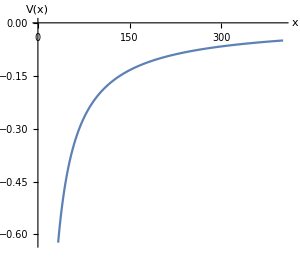

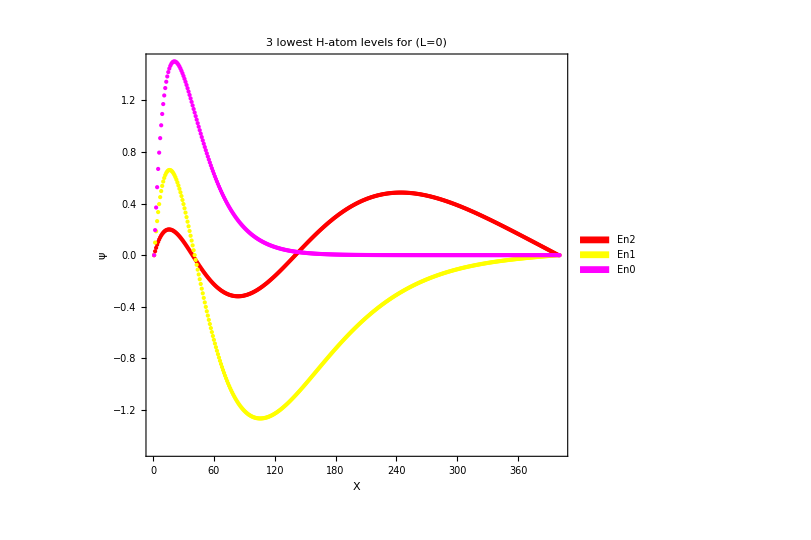

The exact Energies for the first 3 energy eigenvalues for (L=0) are:
 {-0.5,-0.125,-0.0555556}
estimated values from computations using the shooting method were for (L=0):
{-0.499688, -0.124967, -0.0498172}

-Graphics-

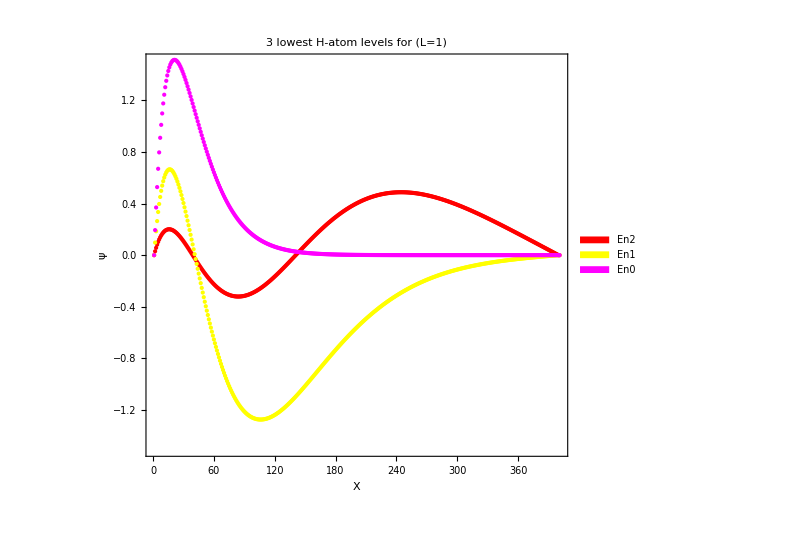

The exact Energies for the first 3 energy eigenvalues  are:
 {-0.5,-0.125,-0.0555556}
estimated values from computations using the shooting method were for (L=1):
{-0.496329, -0.124539, -0.0496301}

```mathematica
(*First part for l= zero*)
ClearAll["Global`*"]
xMax = 20.0; dx =0.05; 
x = Range[0, xMax, dx]; lx = Length[x];
v = Table[-1/i, {i,0.000000000000000000001,xMax,dx}];(*inverse potential for the H atom*)
i0 = 1;

nEng = 3; (* number of energy levels *)
color={Red,Yellow,Magenta};
labels={"En2","En1","En0"};
engOddList = Table[0.0, {i,nEng}];
plot = Table[0.0, {i,nEng}];

eng = -0.001; (* first guess for E *)
psiMax = 2.0; (* top bound for psi *)

Monitor[
Do[
dE = -0.01; (* first guess for dE *) 

(* Obtaining the sign of the initial psi RIGHT*)
psi = Table[0.0, {i,lx}];
psi[[i0]] = 0.0 (*Given initial condition*); psi[[i0 +1]] = 0.00; 
i=i0+2;

(*We need to use the appropriate differential equation here for the psi calculated from the given radial differential equation and using the shooting method*)

While[Abs[psi[[i-1]]] < psiMax && i < lx,
psi[[i]] = 2.0 psi[[i-1]] - psi[[i-2]] +2( v[[i-1]]-eng )psi[[i-1]] dx^2;  i++];
psiLastR=psi[[i-1]] ; (* Last value of psi before quitting *)

(* Main loop for energy levels *)
While[Abs[dE] >0.0000000000000001,
psi = Table[0.0, {i,lx}];
psi[[i0]] = 0.0; psi[[i0 +1]] = 0.0001; 

i=i0+2;
While[Abs[psi[[i-1]]] < psiMax && i < lx,
psi[[i]] = (2.0 psi[[i-1]] - psi[[i-2]] +2( v[[i-1]]-eng )psi[[i-1]] dx^2);  i++];
psiNewR=psi[[i-1]] ;
If[Sign[psiNewR] == Sign[psiLastR], eng = eng - dE]; 
If[Sign[psiNewR] != Sign[psiLastR],dE=-dE/2.0; eng = eng - dE];
psiLastR = psiNewR];
(*---------------------------------------------------------------------*)


engOddList[[-j]] = eng; (*I used -j as an index to reverse the order since it starts to solve from the *)
eng = eng -0.0001;

plot[[j]]=ListPlot[psi*j^1.7 300,PlotRange->All,PlotStyle->{color[[j]],PointSize->0.005},(*I used a j dependent factor for the plot to adjust the relative sizes of each plot seperately- a kind of pseudonormalization*)PlotLegends->SwatchLegend[{color[[j]]},{labels[[j]]}]]
,{j,nEng}],ProgressIndicator[i,{j,nEng}]]
(*---------------------------------------------------------------------------*)


engOddList (* shooting method *);
engExact =Table[-1.0/(2 n^2),{n,3}] //StandardForm;(*exact values for the hydrogen atom*)
ListPlot[v, Joined->True, AxesLabel->{"x","V(x)"},AspectRatio->0.9,ImageSize->300]
Show[plot[[1]],plot[[2]],plot[[3]],PlotRange-> {-1.5,1.5},AspectRatio->0.9,ImageSize->600,Frame -> True, FrameLabel->{Style["X",FontSize->15],Style["ψ",FontSize->20]},PlotLabel->"3 lowest H-atom levels for (L=0)"]

Print["The exact Energies for the first 3 energy eigenvalues for (L=0) are:\n " <>ToString [engExact]<>"\nestimated values from computations using the shooting method were for (L=0):\n" <>ToString[engOddList]]

(*--------------------------------------------------------------------------------------------------------------------------------------------------------------------------*)
(*--------------------------------------------------------------------------------------------------------------------------------------------------------------------------*)
(*--------------------------------------------------------------------------------------------------------------------------------------------------------------------------*)
(*--------------------------------------------------------------------------------------------------------------------------------------------------------------------------*)

(*Second part for l= one*)
ClearAll["Global`*"]
xMax = 20.0; dx =0.05; 
x = Range[0, xMax, dx]; lx = Length[x];
v = Table[-1/i, {i,0.000000000000000000001,xMax,dx}];(*inverse potential for the H atom*)
i0 = 1;

nEng = 3; (* number of energy levels *)
color={Red,Yellow,Magenta};
labels={"En2","En1","En0"};
engOddList = Table[0.0, {i,nEng}];
plot = Table[0.0, {i,nEng}];

eng = -0.001; (* first guess for E *)
psiMax = 2.0; (* top bound for psi *)

Monitor[
Do[
dE = -0.01; (* first guess for dE *) 

(* Obtaining the sign of the initial psi RIGHT*)
psi = Table[0.0, {i,lx}];
psi[[i0]] = 0.0 (*Given initial condition*); psi[[i0 +1]] = 0.00; 
i=i0+2;

(*We need to use the appropriate differential equation here for the psi calculated from the given radial differential equation and using the shooting method*)

While[Abs[psi[[i-1]]] < psiMax && i < lx,
psi[[i]] = 2.0 psi[[i-1]] - psi[[i-2]] +2( v[[i-1]]-eng )psi[[i-1]] dx^2 + psi[[i-1]]*1*(1+1)/(i-1)^2  dx^2;  i++];
psiLastR=psi[[i-1]] ; (* Last value of psi before quitting *)

(* Main loop for energy levels *)
While[Abs[dE] >0.0000000000000001,
psi = Table[0.0, {i,lx}];
psi[[i0]] = 0.0; psi[[i0 +1]] = 0.0001; 

i=i0+2;
While[Abs[psi[[i-1]]] < psiMax && i < lx,
psi[[i]] = (2.0 psi[[i-1]] - psi[[i-2]] +2( v[[i-1]]-eng )psi[[i-1]] dx^2+ psi[[i-1]]*1*(1+1)/(i-1)^2  dx^2);  i++];
psiNewR=psi[[i-1]] ;
If[Sign[psiNewR] == Sign[psiLastR], eng = eng - dE]; 
If[Sign[psiNewR] != Sign[psiLastR],dE=-dE/2.0; eng = eng - dE];
psiLastR = psiNewR];
(*---------------------------------------------------------------------*)


engOddList[[-j]] = eng; (*I used -j as an index to reverse the order since it starts to solve from the *)
eng = eng -0.0001;

plot[[j]]=ListPlot[psi*j^1.7 300,PlotRange->All,PlotStyle->{color[[j]],PointSize->0.005},(*I used a j dependent factor for the plot to adjust the relative sizes of each plot seperately- a kind of pseudonormalization*)PlotLegends->SwatchLegend[{color[[j]]},{labels[[j]]}]]
,{j,nEng}],ProgressIndicator[i,{j,nEng}]]
(*---------------------------------------------------------------------------*)


engOddList (* shooting method *);
engExact =Table[-1.0/(2 n^2),{n,3}] //StandardForm;(*exact values for the hydrogen atom*)
ListPlot[v, Joined->True, AxesLabel->{"x","V(x)"},AspectRatio->0.9,ImageSize->300]
Show[plot[[1]],plot[[2]],plot[[3]],PlotRange-> {-1.5,1.5},AspectRatio->0.9,ImageSize->600,Frame -> True, FrameLabel->{Style["X",FontSize->15],Style["ψ",FontSize->20]},PlotLabel->"3 lowest H-atom levels for (L=1)"]

Print["The exact Energies for the first 3 energy eigenvalues  are:\n " <>ToString [engExact]<>"\nestimated values from computations using the shooting method were for (L=1):\n" <>ToString[engOddList]]
```

## Problem 5

## Problem 6

## Problem 7

## Problem 8

## Problem 9

## Problem 10